```mathematica
f[x_] := (x^2-1)/(x^2-4)
x  /. Solve[f[x] == 0]
Reduce[f[x] > 0]
```

{-1,1}

x<-2||-1<x<1||x>2

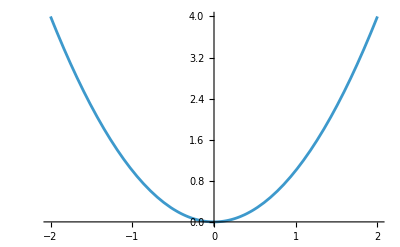

```mathematica
Plot[x^2,{x,-2,2}]
```

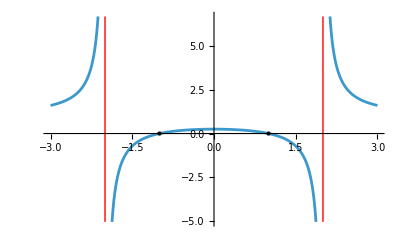

```mathematica
g[x_]:=(x^2-1)/(x^2-4)
Plot[
g[x],
{x,-3,3},
Epilog->{PointSize[Large],Point[{{-1,0},{1,0}}]},
ExclusionsStyle->Red]
```

# Risanje in reševanje enačb z Mathematico

Vaje v tem zvezku pogosto vsebujejo povezavo na dokumentacijo funkcije, ki jo morate uporabiti. Priporočamo, da dokumentacijo vsaj preletite. Včasih navodila omenijo dodatne nastavitve, tudi te poiščite v dokumentaciji.

Spodnja dva primera ilustrirata obe vrsti prirejanja.

```mathematica
(* Takojšnje prirejanje *) (* Vrednost izraza na desni se izračuna in shrani v spremenljivko na desni. Vrednost v spremenljivki ostane enaka. *)
f1=RandomInteger[{0,10}];
f1
f1
f1
```

3

3

3

```mathematica
(* Zakasnjeno prirejanje *)
(* V spremenljivko se shrani izraz na desni, njegova vrednost pa se izračuna vsakič, ko pogledamo, kakšna vrednost je v spremenljivki. *)
f2:=RandomInteger[{0,10}];
f2
f2
f2
```

2

1

7

## Funkcije in njihovi grafi

### Subsection. naloga:

1. Definirajte funkcijo f spremenljivke x s funkcijskim predpisom (x^2-1)/(x^2-4).
2. S funkcijo Plot narišite njen graf na intervalu [-5,5]. Označite še njene pole, tako da dodate nastavitev ExclusionsStyle→{{Dashed,Red}}
3. S funkcijo Solve poiščite ničle in pole funkcije f. Pri polih vam bo prišla prav še funkcija Denominator.
4. Izračunajte levo limito enega izmed polov (funkciji Limit dodate še nastavitev Direction→1).
5. Izračunajte limito funkcije, ko gre .
6. Določite stacionarne točke.
7. S funkcijo Reduce določite intervale konveksnosti (ko velja )
Za vajo lahko doma na podoben način analizirate tudi funkcijo g(x)=arctg x^2/(x^2-1).

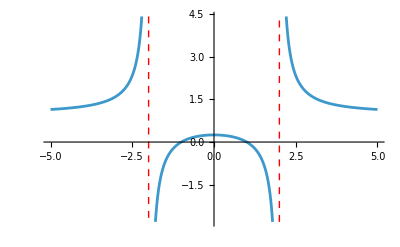

-4+x^2

{-1,1}

{-2,2}

∞

1

{0}

x<-2||x>2

```mathematica
ClearAll[f, d, x];
(*1. naloga*)
f[x_] := (x^2-1)/(x^2-4);
(*2. naloga*)
Plot[
f[x],
{x, -5, 5},
ExclusionsStyle->{{Dashed, Red}}
]
(*3. naloga*)
d[x_] = Denominator[f[x]]
x /. Solve[f[x] == 0]
x /. Solve[d[x] == 0]
(*4. naloga*)
Limit[f[x], x -> -2, Direction->"FromBelow"]
(*5. naloga*)
Limit[f[x], x -> Infinity]
(*6. naloga*)
x /. Solve[f'[x] == 0]
(*7. naloga*)
Reduce[f''[x] > 0]
```

### Subsection. naloga:

1. Dana je parametrično podana krivulja (((3-t) sin t)/(t+1),cos (t) sin (2t)). Definirajte jo kot funkcijo ene spremenljivke.
2. Narišite krivuljo k za  t∈[0,5] s pomočjo funkcije ParametricPlot.
3. Krivulja seče samo sebe natanko dvakrat. S pomočjo numeričnega reševanja enačb (FindRoot) poišči približek presečišč. Enačbo nastavi tako da izenačiš krivuljo, parametrizirano s parametrom t, s krivuljo, parametrizirano s parametrom s. Potem s spreminjanjem začetnih približkov parametrov t in s poskusi določiti vrednosti parametrov, pri katerih pride do samopresečič (dovolj bodo celoštevilske vrednosti, od katerih bo ena enaka 0).

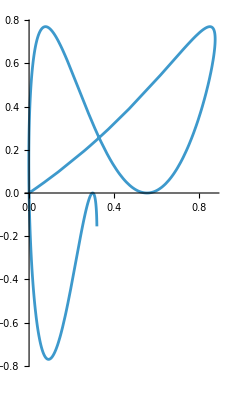

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{t→0.126678,s→4.68299}

{0.322199,0.248646}

```mathematica
ClearAll[f, x]
(*1. naloga*)
f[t_] := {((3-t) Sin[t])/(t + 1), Cos[t] Sin[2 t]};
(*2. naloga*)
ParametricPlot[f[t], {t, 0, 5}]
(*3. naloga*)
x = FindRoot[f[t]==f[s],{t,0.12},{s,4}]
f[t] /. x
```

### Subsection. naloga:

1. Definirajte funkcijo  g(x)=-x^3+8.
2. Narišite njen graf nad intervalom [-3,3] in ga shranite v spremenljivko graf1.
3. Izračunajte ničlo funkcije g (če želite samo realne ničle, funkciji Solve dodajte kot drugi parameter Reals).
4. Izračunajte ploščino lika, ki ga (v prvem kvadrantu) omejujeta koordinatni osi in graf te funkcije.
5. V spremenljivko  graf2 shranite graf funkcije nad intervalom, po katerem ste integrirali. Grafu dodajte določilo Filling→Axis.
6. Postavite oba grafa na isti koordinatni sistem s funkcijo Show.

{{x→2}}

12

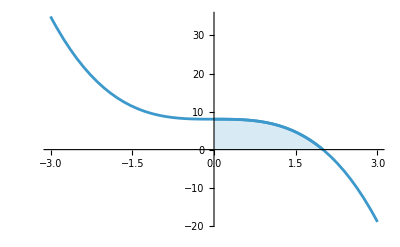

```mathematica
ClearAll[g, graf1, zeros]
(*1. naloga*)
g[x_] := -x^3+8;
(*2. naloga*)
graf1 = Plot[
g[x],
{x,-3,3}
];
(*3. naloga*)
zeros = Solve[g[x] == 0, x, Reals]
(*4. naloga*)
Integrate[g[x], {x, 0, 2}]
(*5. naloga*)
graf2 = Plot[
g[x],
{x, 0, 2},
Filling->Axis
];
(*6. naloga*)
Show[graf1, graf2]
```

### Subsection. naloga:

1. Definiraj funkciji  s(x)=x^2-8  in  z(x)=-x^2+10  ter nariši njuna grafa. Funkcija Plot bo narisala več grafov, če jih podate naštete v seznamu (v zavitih oklepajih, ločene z vejicami).
2. Poiščite njuni presečišči.
3. Izračunajte ploščino lika, ki ga omejujeta grafa teh dveh funkcij.
4. Še enkrat narišite grafa obeh funkcij, le da bo tokrat območje, katerega ploščino ste izračunali, pobarvano. Filling nastavite na {1→{2}} (kaj to naredi, poiščite v dokumentaciji nastavitve pod Applications).

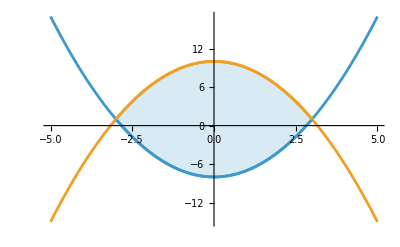

```mathematica
ClearAll[s, z, x];
(*1. naloga*)
s[x_] = x^2-8;
z[x_] = -x^2+10;
graf1 = Plot[
{s[x], z[x]},
{x, -5, 5}
];
(*2. naloga*)
xs = Solve[s[x] == z[x], x];
x /. xs;
y = s[x] /. xs;
(*3. naloga*)
Integrate[z[x]-s[x], {x, -3, 3}];
(*4. naloga*)
graf2 = Plot[
{s[x], z[x]},
{x, -3, 3},
Filling->{1->{2}}
];
Show[graf1, graf2]
```

## Reševanje enačb

### Subsection. naloga:

1. Numerično izračunaj ničle polinoma  x^7-2 x^6-x^5-2 x^4+12 x^2-x+1. 
2. Preberite dokumentacijo funkcije NSolve in izračunajte samo realne ničle.

```mathematica
ClearAll[p];
p =  x^7-2x^6-x^5 - 2x^4 + 12x^2 - x + 1 
NSolve[p, x]
NSolve[p, x, Reals]
```

1-x+12 x^2-2 x^4-x^5-2 x^6+x^7

{{x→-1.37527},{x→-0.356206-1.47367 ⅈ},{x→-0.356206+1.47367 ⅈ},{x→0.040941-0.283889 ⅈ},{x→0.040941+0.283889 ⅈ},{x→1.59494},{x→2.41086}}

{{x→-1.37527},{x→1.59494},{x→2.41086}}

### Subsection. naloga:

Določi vsa realna števila, ki zadoščajo neenačbi  (|x-3|)/(x+1)>√(3-2x)

```mathematica
ClearAll[f, g];
f[x_] := Abs[x-3]/(x+1);
g[x_] := Sqrt[3 - 2 x];
Reduce[f[x] > g[x], x, Reals]
```

-1<x<1||1<x≤3/2

### Subsection. naloga:

S funkcijo Solve rešujemo enačbe. Najbolj enostavno jo uporabimo, kadar imamo opravka z eno samo spremenljivko:
- Poiščite vsa kompleksna števila, ki zadoščajo enačbi  z̄=z^2. Za konjugiranje lahko uporabite *, funkcijo Conjugate ali pa znak Esc co Esc.
- Določite vrednost parametra a v enačbi (2a x+3a)/(3a + 5x)=(3a-4)/(3a - 5x), da bo  x=2  rešitev enačbe.

```mathematica
ClearAll[z, x, a];
(*1. naloga*)
Solve[z*==z^2, z, Complexes]

(*2. naloga*)
x = 2;
Solve[(2 a x + 3 a)/(3 a + 5 x)==(3 a - 4)/(3 a - 5 x), a]
```

{{z→0},{z→1},{z→-1/2-(ⅈ √3)/2},{z→-1/2+(ⅈ √3)/2}}

{{a→1/3 (11-√91)},{a→1/3 (11+√91)}}

### Subsection. naloga:

Rešujemo lahko tudi več enačb z več neznankami. V tem primeru enačbe naštejemo v zavite oklepaje (ločene naj bodo z vejicami).
Določite k in n tako, da bo šla premica y=k x+n skozi točki (-2,3) in (6,-1).

```mathematica
ClearAll[k, n, f, x];
Solve[
{3 == -2 k + n, -1 == 6 k + n},
{k, n}
]
```

{{k→-1/2,n→2}}

### Subsection. naloga:

Sin je 3 leta starejši od hčere, mati pa je 23 let starejša od sina. Pred 6 leti je imela mati 4 krat toliko let kot sin in hči skupaj. Koliko je star vsak od njih? Napišite enačbe in jih rešite s pomočjo funkcije Solve.

```mathematica
Solve[
{h == s - 3,
m == s + 23,
m - 6 == 4 ((h - 6) + (s - 6))
},
{h, s, m}
]
```

{{h→8,s→11,m→34}}

### Subsection. naloga:

Koliko začetnih členov zaporedja s splošnim členom  a_n=16-2n  moramo sešteti, da bo vsota enaka 36? Začnite s tem, da napišete vsoto ∑_(i=1)^k a_i, nato pa ustrezno enačbo.

```mathematica
ClearAll[s, a];
a[n_] := 16 - 2 n;
s[k_] := Sum[a[n], {n, 1, k}];
Solve[s[k] == 36, k]
```

{{k→3},{k→12}}